# Homework 3

## Exercise 1

### Non-mathematica

P_A = f(c_A, P_B)
P_B = g(c_B, P_A)

dP_A = f_C_AⅆC_A+ f_P_BⅆP_B
dP_B = g_C_BⅆC_B+ g_P_AⅆP_A
where h_x = (∂h)/(∂x)

We can rewrite these as:
ⅆ P_A - f_P_B ⅆ P_B  = f_C_A ⅆ C_A
ⅆ P_B - g_P_A ⅆ P_A = g_C_B ⅆ C_B

Or in matrix form:
(1 | -f_P_B
-g_P_A | 1) (ⅆ P_A
ⅆ P_B) = (f_C_A ⅆ C_A
g_C_B ⅆ C_B)

If we invert the matrix of coefficients we obtain

1/Δ (1 | f_P_B
g_P_A | 1), where Δ = 1 - (f_P_B) (g_P_A)

Multiplying by the inverse, we obtain
(ⅆ P_A
ⅆ P_B) = 1/Δ (1 | f_P_B
g_P_A | 1) (f_C_A ⅆ C_A
g_C_B ⅆ C_B)

(ⅆ P_A
ⅆ P_B) = 1/Δ (f_C_A ⅆ C_A + f_P_B g_C_B ⅆ C_B
g_P_A f_C_A ⅆ C_A + g_C_B ⅆ C_B)

The comparative statics are as follows (assuming, (ⅆ C_B)/(ⅆ C_A) = 0, (ⅆ C_A)/(ⅆ C_B) = 0):

(ⅆ P_A)/(ⅆ C_A) = f_C_A + f_P_B (g_C_B(ⅆ C_B)/(ⅆ C_A)+ g_P_A (ⅆ P_A)/(ⅆ C_A))
(ⅆ P_A)/(ⅆ C_A) = f_C_A + f_P_B g_P_A (ⅆ P_A)/(ⅆ C_A)
(ⅆ P_A)/(ⅆ C_A) -  f_P_B g_P_A (ⅆ P_A)/(ⅆ C_A) = f_C_A
((ⅆ P_A)/(ⅆ C_A)) (1 -  f_P_B g_P_A) =  f_C_A
(ⅆ P_A)/(ⅆ C_A)=  f_C_A/(1-f_P_B g_P_A)
Similarly
(ⅆ P_B)/(ⅆ C_B)=  f_C_B/(1-g_P_B f_P_A)

(ⅆ P_A)/(ⅆ C_B) = f_C_A (ⅆ C_A)/(ⅆ C_B) + f_P_B(g_C_B + g_P_A (ⅆ P_A)/(ⅆ C_B))
(ⅆ P_A)/(ⅆ C_B) = f_P_B(g_C_B + g_P_A (ⅆ P_A)/(ⅆ C_B))
(ⅆ P_A)/(ⅆ C_B) - g_P_A (ⅆ P_A)/(ⅆ C_B)= f_P_Bg_C_B
((ⅆ P_A)/(ⅆ C_B)) (1 - g_P_A) = f_P_Bg_C_B
(ⅆ P_A)/(ⅆ C_B) = (f_P_B g_C_B)/(1-g_P_A)
Similarly
(ⅆ P_B)/(ⅆ C_A) = (g_P_A f_C_A)/(1-f_P_B)

Assuming
f_C_A ≥ 0 (Firm A increases [weakly] prices due to higher production costs)
f_P_B ≥ 0 (Firm A increases [weakly] prices due to higher prices from firm B)
g_C_B ≥ 0 (Firm B increases [weakly] increases prices due to higher production costs)
g_P_A ≥ 0 (Firm B increases [weakly] prices due to higher prices from firm A)

We obtain the following signs
(ⅆ P_A)/(ⅆ C_A) ≥ 0
(ⅆ P_B)/(ⅆ C_B) ≥ 0
(ⅆ P_A)/(ⅆ C_B) ≥ 0
(ⅆ P_B)/(ⅆ C_A) ≥ 0

### Mathematica

## Exercise 2

Maximize x^0.5 y^0.5 such that 2 x + y = k

ℒ (x, y, λ) = x^0.5 y^0.5 + λ (2 x + y - k)

(∂ℒ)/(∂x) = (√y)/(2√x) + 2 λ = 0
(∂ℒ)/(∂y) = ((√x)/(2√y)) + λ = 0
(∂ℒ)/(∂λ) = 2 x + y - k = 0

λ = (-√x)/(2√y)
2 λ =  (-√x)/(√y)
(∂ℒ)/(∂x) = ((√y)/(2 √x)) - (√x)/(√y) = 0
((√y)/(2 √x)) = (√x)/(√y)
y = 2 x
-2 x + y = 0

2 x + y - k = 0
2x + y = k

(-2 | 1
2 | 1) (x
y) = (0
k)

(x
y) = (-1/4 | 1/4
1/2 | 1/2) (0
k) = (-1/4 0+1/4 k
1/2 0 + 1/2 k)
(x
y)  = (k/4
k/2)

## Exercise 3

C(n + 1, k + 1) = ((n + 1)!)/((k + 1)! (n - k)!)
C(n, k) = (n!)/(k!(n-k)!) = (n!)/(k! (n - k) (n-k -1)!) = (n!)/(k! (n - k - 1)!) 1/(n - k)
C(n, k + 1) = (n!)/((k + 1)! (n - k -1)!) = (n!)/((k + 1) k! (n - k - 1)!) = (n!)/(k! (n - k -1)!) 1/(k + 1)
C(n, k) + C(n, k + 1) = (n!)/(k! (n - k -1)!) 1/(k + 1) + (n!)/(k! (n - k - 1)!) 1/(n - k) = (n!)/(k! (n - k -1)!) (1/(k + 1) + 1/(n - k))
= (n!)/(k! (n - k -1)!) ((n - k + k + 1)/((k + 1)(n-k))) = (n!)/(k! (n - k -1)!) ((n + 1)/((k + 1)(n-k))) = ((n + 1)!)/((k + 1)! (n - k)!) = C(n + 1, k + 1)

## Exercise 4

asa

## Exercise 5

asa

## Exercise 6

asa

## Computational Exercise 1

```mathematica
ClearAll[lst, x, l, square, newList]
lst = Range[0, 15]
newList = {};
Do[AppendTo[newList, x^2], {x, lst}];
StringForm["The squared list using loops: ``", newList]
square [l_]:= (
y = {};
Do[AppendTo[y, x^2],{x, l}];
Return[y]
)
StringForm["The squared list using a function: ``", square[lst]]
StringForm["The squared list using map: ``", Map[#^2&, lst]]
isEven[x_] := If[EvenQ[x], 1, 0]
isEven[9]
isEven[10]
Pick[lst, Map[isEven, lst], 1]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

The squared list using loops: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

The squared list using a function: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

The squared list using map: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

0

1

{0,2,4,6,8,10,12,14}

## Computational Exercise 2

```mathematica
ClearAll[powerSet, x, y, subsets]
powerSet[s_List] := (
subsets = {{}};
Do[(
newSubsets = {};
Do[(
newSubset = Union[oldSubset, {element}]; 
AppendTo[newSubsets, newSubset];
),{oldSubset, subsets}
];
subsets = Join[subsets, newSubsets];
), {element, s}];
Return[subsets]
)
powerSet[{e1, e2, e3}]
```

{{},{e1},{e2},{e1,e2},{e3},{e1,e3},{e2,e3},{e1,e2,e3}}

## Computational Exercise 3

```mathematica
asa
```

## Computational Exercise 4

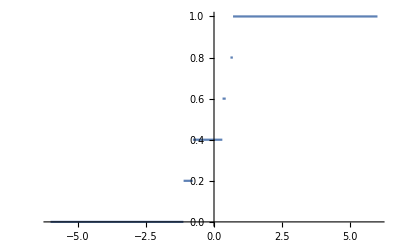

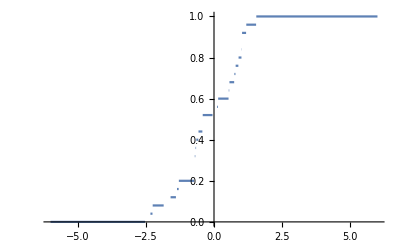

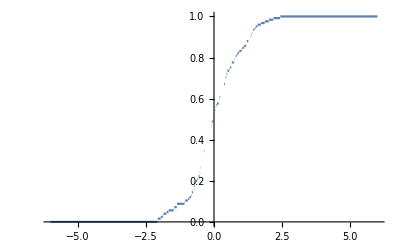

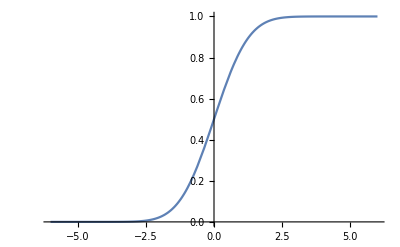

```mathematica
fiveDraws = RandomVariate[NormalDistribution[],5]; (* Take five draws *)
twentyFiveDraws = RandomVariate[NormalDistribution[],25]; (* Take twenty five draws *)
oneTwentyFiveDraws = RandomVariate[NormalDistribution[],125]; (* Take one hunder and twenty five draws *)
d5 = EmpiricalDistribution[fiveDraws]; (* Convert to a random distribution *)
d25 = EmpiricalDistribution[twentyFiveDraws]; (* Convert to a random distribution *)
d125 = EmpiricalDistribution[oneTwentyFiveDraws]; (* Convert to a random distribution *)
(* Plot *)
Plot[CDF[d5, x], {x, -6, 6}]
Plot[CDF[d25, x], {x, -6, 6}]
Plot[CDF[d125, x], {x, -6, 6}]
Plot[CDF[NormalDistribution[],x], {x, -6, 6}]
```